```mathematica
alpha1 = (1/0.86)^2;
alpha2 = (1/0.45)^2;
dist = TransformedDistribution[u+v,{u\[Distributed]GammaDistribution[alpha1,5.1/alpha1],v\[Distributed]GammaDistribution[alpha2,18.8/alpha2]}];
lst = {}
```

{}

```mathematica
For[i=0,i<=200,i++,AppendTo[lst,PDF[ dist, i]]]
For[i=1,i<=201,i++,lst[[i]] = Round[lst[[i]], 0.000001]]
```

```mathematica
Export["/Users/Jake/Desktop/Current Classes/CS 156b/firewall-covid/Imperial College Model/PiDistribution.csv",lst,"csv"];
```

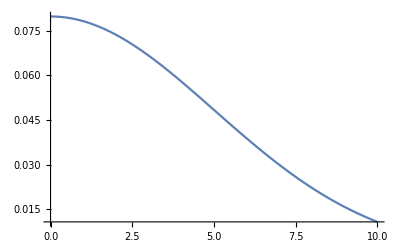

```mathematica
Plot[PDF[NormalDistribution[0, 5], x], {x, 0, 10}]
```